```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\85F11"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,10]
,16,0.00002],1500<#[[1]]<4500&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.361},{loc[[-1,1]],-0.361/2}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,10],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],10],GaussianFilter[20data2[[i]][[All,4]],10],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],10]
,16,0.00002],1500<#[[1]]<4500&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,62},1,Length[data2],1}]
```

ListPlot::lpn: {{{1.,0.208707},{2.,0.208622},{3.,0.208527},{4.,0.208444},{5.,0.20834},{6.,0.208256},{7.,0.208159},{8.,0.208088},{9.,0.208011},{10.,0.207965},{11.,0.207915},{12.,0.207898},{13.,0.207898},{14.,0.207929},«23»,{38.,0.208931},{39.,0.208907},{40.,0.208874},{41.,0.208855},{42.,0.208821},{43.,0.208815},{44.,0.208789},{45.,0.208787},{46.,0.208748},{47.,0.208749},{48.,0.20875},{49.,0.20875},{50.,0.20875},«6200»},{«1»},{}} is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],Joined->True,Epilog->Line[{{-2,1},{2,1}}]],{{i,48},1,Length[data2],1}]
```

```mathematica
power
```

{0.5,0.5,0.5,0.5,1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,5,5,5,5,6,6,6,6,7,7,7,7,8,8,8,8,9,9,9,9,10,10,10,10,15,15,15,15,20,20,20,20,25,25,25,25,30,30,30,30,35,35,35,35,40,40,40,40,50,50,50,50,60,60,60,60,70,70,70,70,80,80,80,80}

```mathematica
power[[45]]
```

15

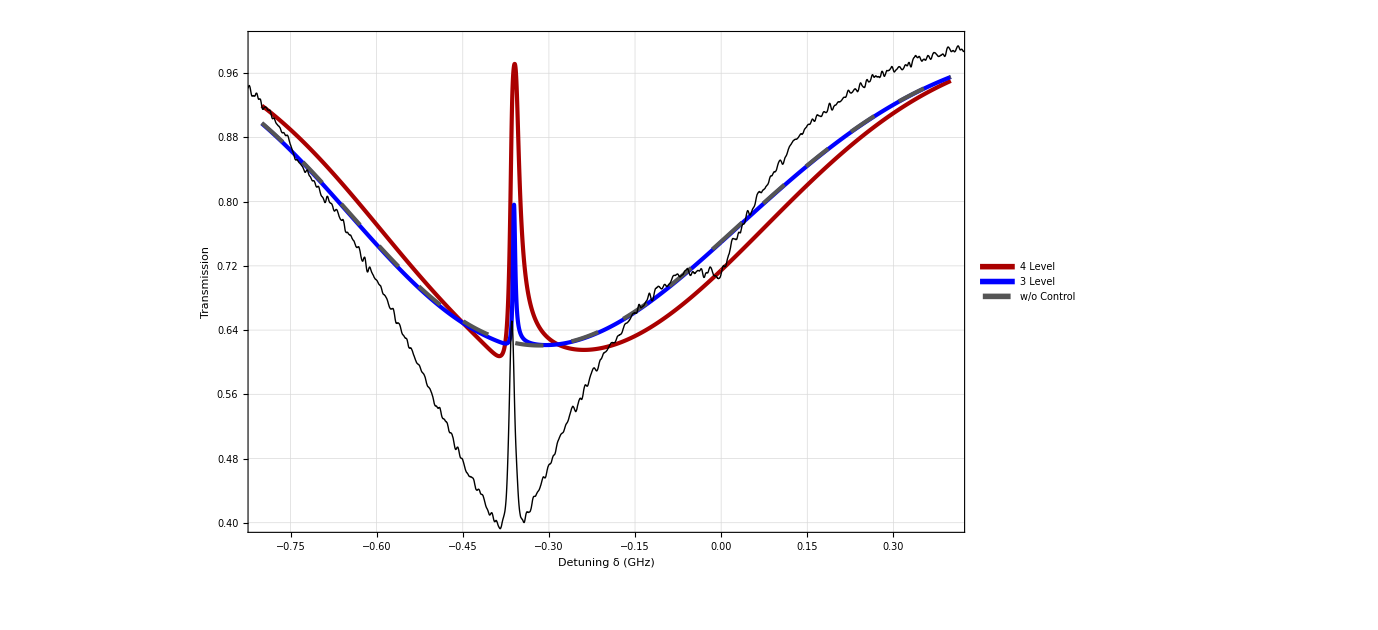

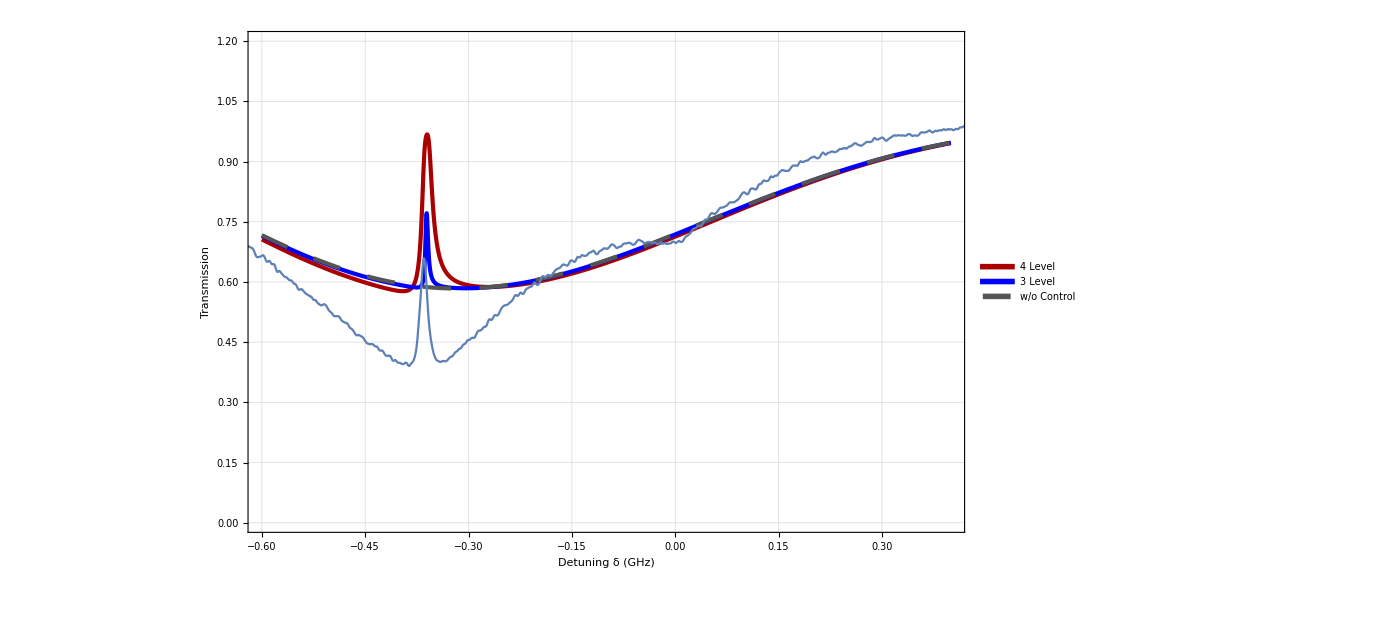

```mathematica
final2=ListPlot[{Lev4DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,-361*10^6,0],Lev3DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,-361*10^6,0],Lev3DoppTestsc[23,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Darker[Gray],Dashing[.02]},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.8,0.4},{0.4,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[45]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
```

```mathematica
Manipulate[ListPlot[Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&]],{i,1,Length[data2],1}]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmax7711=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&][[All,2]]//Max,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Max],{i,1,Length[data],1}];
```

```mathematica
EITmin7711=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.005-0.361<#[[1]]<0.02-0.361&][[All,2]]//Min,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Min],{i,1,Length[data],1}];
```

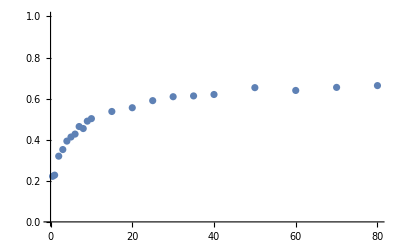

```mathematica
rb8511=ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax7711,4]]/Log[Min/@Partition[EITmin7711,4]]}]},PlotRange->{0,1}]
```

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\85F11\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```

```mathematica
Table[Select[Transpose[f[data2off[[1]]][[{4,2}]]],-0.02<#[[1]]<0.02&][[All,2]]//Min,{i,1,Length[dataoff],1}]//Mean
```

0.487031

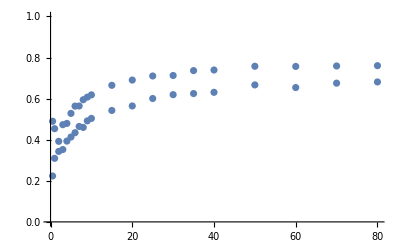

```mathematica
Show[rb8511,rb8711]
```